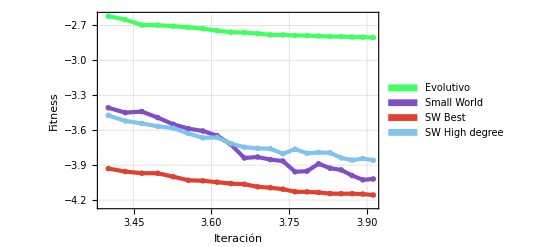

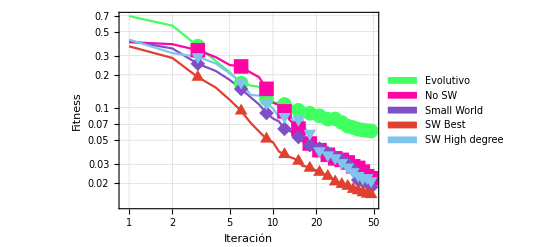

```mathematica
evolutivo = {0.693830637,0.566824452,0.367541776,0.268107296,0.21098871,0.167758457,0.159246619,0.15526797,0.119793955,0.111724129,0.10963834,0.106799367,0.105489223,0.102886134,0.094313197,0.09231484,0.090912071,0.088558349,0.088067992,0.085544736,0.083920962,0.083241573,0.082029021,0.078162258,0.07943573,0.078700916,0.07853244,0.076457843,0.073255494,0.072830114,0.070657763,0.067484897,0.067402369,0.066770264,0.066185245,0.065398856,0.064253416,0.063427374,0.063218243,0.062700618,0.061984767,0.061984767,0.061674381,0.061616538,0.061369607,0.061121187,0.061084798,0.06081927,0.060800177,0.06055252};
nosw = {0.399545726,0.382709935,0.336799873,0.290698991,0.246313756,0.23887238,0.209618459,0.18981243,0.148570747,0.110454248,0.10562073,0.092145799,0.077061061,0.070247379,0.063886582,0.050900307,0.048234868,0.046610539,0.043395251,0.040842364,0.040492248,0.04046607,0.039237744,0.036730355,0.036169249,0.035271958,0.034048118,0.0343537,0.033960167,0.032965139,0.031866465,0.031762796,0.031233447,0.031218494,0.030094845,0.028759188,0.02895862,0.027813293,0.027804976,0.026525598,0.025801988,0.0257255,0.025145426,0.024684469,0.023296154,0.023095147,0.022996448,0.022312934,0.022032263,0.021737638};
sw={0.41124199,0.34930179,0.252896707,0.216890581,0.179510578,0.147971248,0.124138232,0.106504874,0.088975981,0.079243287,0.07428944,0.06360616,0.061088654,0.057287525,0.053513041,0.048771915,0.04714676,0.044986415,0.045622858,0.044184184,0.041892742,0.041751588,0.040004584,0.038119173,0.037298919,0.035614655,0.034633205,0.035753135,0.034824264,0.033141392,0.031767021,0.032073076,0.030459009,0.028744056,0.027703275,0.027146619,0.026073255,0.024172723,0.02151993,0.021705837,0.021226575,0.020965135,0.019116478,0.019220917,0.020479074,0.019713769,0.019424862,0.01850665,0.01784028,0.017969451};
swbest = {0.365565974,0.285572748,0.190373246,0.152537262,0.117619557,0.09313062,0.071983833,0.060093427,0.051399095,0.04776188,0.039256938,0.037004863,0.035061114,0.033915607,0.032127419,0.028980845,0.028653362,0.027708514,0.026929519,0.026409925,0.025405942,0.02492448,0.024093712,0.023314611,0.023161258,0.021556436,0.020741067,0.020425726,0.020308295,0.019651384,0.019149433,0.018887705,0.01887197,0.018324683,0.017777061,0.017692386,0.017483211,0.017269666,0.017179813,0.016801673,0.016666911,0.016462926,0.016101197,0.016084552,0.016002721,0.015844981,0.015832234,0.015833862,0.015785159,0.015658185};
swhd ={0.421636917,0.317028026,0.292959372,0.254266749,0.206294542,0.17041676,0.130596105,0.12877724,0.109697445,0.097799182,0.081319648,0.082432053,0.084588537,0.073669023,0.07753019,0.078047605,0.06135903,0.057798847,0.046499356,0.044607752,0.03984671,0.037822568,0.037059671,0.036543802,0.036036781,0.036247257,0.034330149,0.033430566,0.032534494,0.031031902,0.029580634,0.028969524,0.028260764,0.027810627,0.026585261,0.025588037,0.025680089,0.02433955,0.023606687,0.023392912,0.023311284,0.022326455,0.023222979,0.022419437,0.022571206,0.022505616,0.021549661,0.021124706,0.021418167,0.021105568};

ListLogLogPlot[{evolutivo[[30;;50]],sw[[30;;50]],swbest[[30;;50]],swhd[[30;;50]]},Joined->True,PlotRange->Full, DataRange->{30,50}, GridLines->Automatic, FrameTicksStyle->Directive[Black,15],Frame->{{True,False},{True,False}},FrameLabel->{Style["Iteración",Black,Large],Style["Fitness",Black,Large]},PlotLegends->SwatchLegend[{"Evolutivo","Small World","SW Best","SW High degree"}], PlotTheme->"Business", PlotStyle->{RGBColor[0.25,1,0.38],RGBColor[0.5,0.31,0.78], RGBColor[0.88,0.25,0.18],RGBColor[0.5,0.77,0.93]}]

ListLogLogPlot[{evolutivo,nosw,sw,swbest,swhd},Joined->True,PlotRange->Full,GridLines->Automatic, FrameTicksStyle->Directive[Black,15], Frame->{{True,False},{True,False}},FrameLabel->{Style["Iteración",Black,Large],Style["Fitness",Black,Large]},PlotLegends->SwatchLegend[{"Evolutivo","No SW","Small World","SW Best","SW High degree"}],Mesh->{Range[0,50,3]},PlotMarkers->{Automatic,15},PlotStyle->{RGBColor[0.25,1,0.38],RGBColor[1,0.01,0.65],RGBColor[0.5,0.31,0.78], RGBColor[0.88,0.25,0.18],RGBColor[0.5,0.77,0.93],Thickness[0.008]}]
```